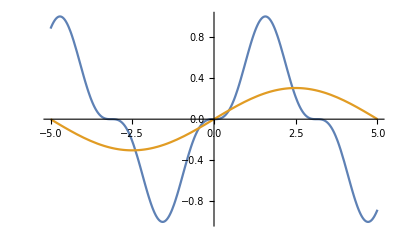
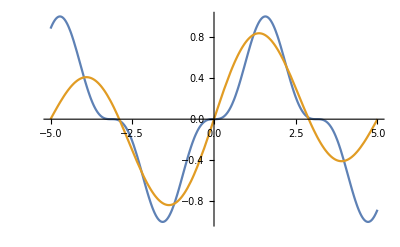
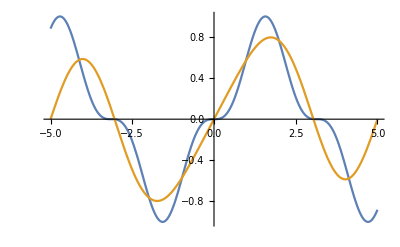
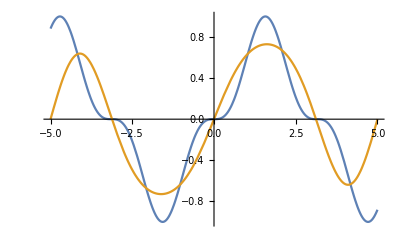
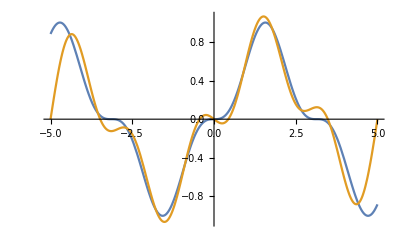
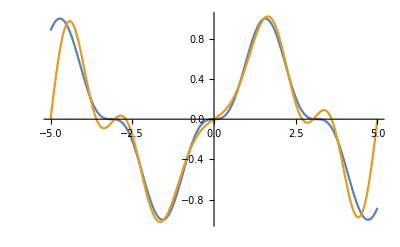
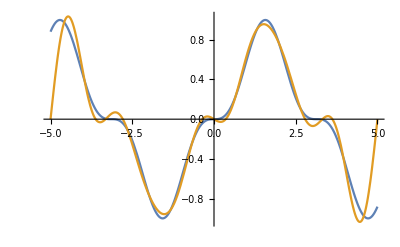
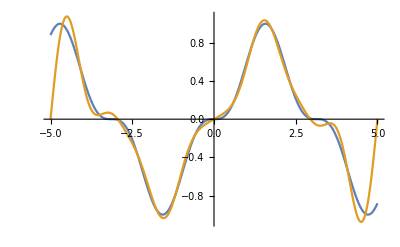

```mathematica
f[x_]:=Sin[x]^3;

L=5;
a[0]=1/(2L)∫_-L^L f[x]ⅆx;
a[n_]=1/L∫_-L^L (f[x]*Cos[(n π x)/L])ⅆx;
b[n_]=1/L∫_-L^L (f[x]*Sin[(n π x)/L])ⅆx;
g[x_,nmax_]:=a[0]+∑_(n=1)^nmax (a[n]*Cos[(n π x)/L]+b[n]*Sin[(n π x)/L]);
Table[
Plot[{f[x],g[x,pr]},{x,-L,L}],{pr,1,10}]
```